# Conos de luz

## Schwarzschild 5D

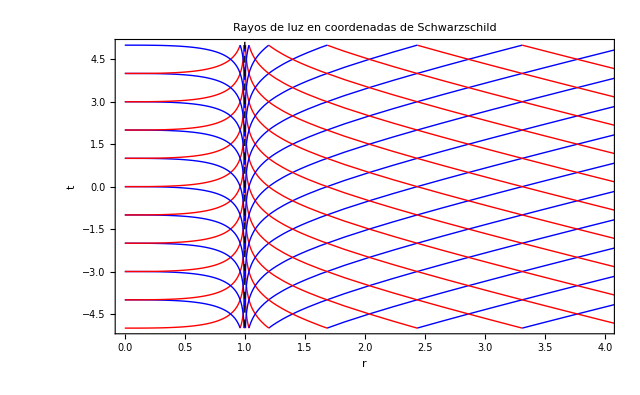

```mathematica
(*Definición de parámetros*)
μ=1; (*Masa del agujero negro*)
rh=Sqrt[μ]; (*Radio del Horizonte*)

(*Coordenada de tortuga r**)
rStar[r_]:=r+(rh/2)*Log[Abs[(r-rh)/(r+rh)]];

(*Trayectorias de luz en Schwarzschild 5D(t vs r)*)
(*t=constant\pm r**)
plotSchwarzschild5D=Plot[Evaluate[Table[{rStar[r]+c,-rStar[r]+c},{c,-10,10,1}]],{r,0,10},PlotRange->{{0,4},{-5,5}},PlotStyle->{Directive[Blue,Thin],Directive[Red,Thin]},Frame->True,FrameLabel->{"r","t"},PlotLabel->"Rayos de luz en coordenadas de Schwarzschild",Epilog->{Dashed,Black,InfiniteLine[{rh,0},{0,1}]}]
```

```mathematica
Export["Conos de Luz Sch5D.png",plotSchwarzschild5D]
```

Conos de Luz Sch5D.png

## Gauss-Bonnet 5D

```mathematica
Clear["Global`*"]
```

0.707107

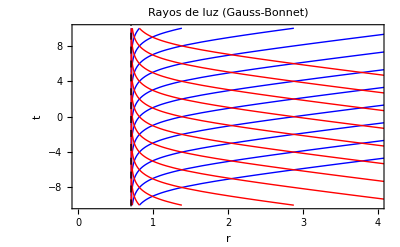

```mathematica
μ=2;

(*Función métrica Gauss-Bonnet (rama física)*)
f[r_]:=1+r^2-Sqrt[r^4+μ];
(*Encontrar el horizonte*)
rh=r/. FindRoot[f[r]==0,{r,1}]
(*Coordenada tortuga como solución de EDO*)rStarFunc=NDSolveValue[{y'[r]==1/f[r],y[rh+0.001]==0},y,{r,rh+0.000001,10},MaxStepSize->0.01];
(*Rayos de luz:t=±r*+c*)plotGB=Plot[Evaluate[Table[{rStarFunc[r]+c,-rStarFunc[r]+c},{c,-15,15,2}]],{r,rh+0.001,10},PlotRange->{{0,4},{-10,10}},PlotStyle->{Directive[Blue,Thin],Directive[Red,Thin]},Frame->True,FrameLabel->{"r","t"},PlotLabel->"Rayos de luz (Gauss-Bonnet)",Epilog->{Dashed,Black,InfiniteLine[{rh,0},{0,1}]}]
```

```mathematica
Export["Conos de Luz GB5D.png",plotGB]
```

Conos de Luz GB5D.png

## Tercer orden en la curvatura

### Acoplamiento α^2

```mathematica
Clear["Global`*"]
```

{0.153958,0.954716}

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

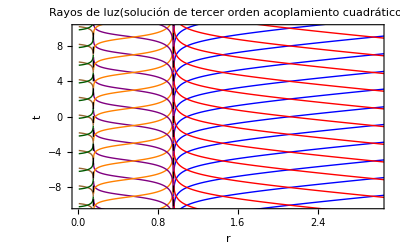

```mathematica
μ=1;

(*Función métrica de tercer orden*)
f[r_]:=1+r^2-(101 r^4)/(7^(1/3) (-1085 r^6-1134 r^2 μ+18 √7 r^2 √(3699 r^8+1085 r^4 μ+567 μ^2))^(1/3))+1/7 (-7595 r^6-7938 r^2 μ+126 √7 r^2 √(3699 r^8+1085 r^4 μ+567 μ^2))^(1/3)
(*Buscar ambas raíces*)
horizons=r/. NSolve[f[r]==0&&r<10&&r>0,r,Reals];
{rInner,rOuter}=Sort[horizons]
rStarExt=NDSolveValue[{y'[r]==1/f[r],y[rOuter+0.001]==0},y,{r,rOuter+0.001,10}];
rStarMid=NDSolveValue[{y'[r]==1/f[r],y[(rInner+rOuter)/2]==0},y,{r,rInner+0.001,rOuter-0.001}];
rStarInt=NDSolveValue[{y'[r]==1/f[r],y[rInner-0.001]==0},y,{r,0.001,rInner-0.001}];
plotExt=Plot[Evaluate[Table[{rStarExt[r]+c,-rStarExt[r]+c},{c,-15,15,2}]],{r,rOuter+0.001,4},PlotStyle->{Directive[Blue,Thin],Directive[Red,Thin]}];
plotMid=Plot[Evaluate[Table[{rStarMid[r]+c,-rStarMid[r]+c},{c,-15,15,2}]],{r,rInner+0.001,rOuter-0.001},PlotStyle->{Directive[Purple,Thin],Directive[Orange,Thin]}];
plotInt=Plot[Evaluate[Table[{rStarInt[r]+c,-rStarInt[r]+c},{c,-15,15,2}]],{r,0.001,rInner-0.001},PlotStyle->{Directive[DarkGreen,Thin],Directive[Brown,Thin]}];
plotf3cuad=Show[plotExt,plotMid,plotInt,Frame->True,FrameLabel->{"r","t"},PlotRange->{{0,3},{-10,10}},PlotLabel->"Rayos de luz(solución de tercer orden acoplamiento cuadrático)",Epilog->{{Dashed,Black,InfiniteLine[{rOuter,0},{0,1}]},{Dashed,Black,InfiniteLine[{rInner,0},{0,1}]}}]
```

```mathematica
Export["Conos de Luz f3cuad5D.png",plotf3cuad]
```

Conos de Luz f3cuad5D.png

### Acoplamiento b=4

```mathematica
Clear["Global`*"]
```

{0.0743047,0.989078}

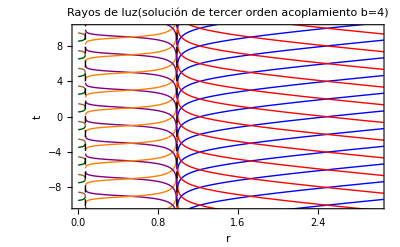

```mathematica
μ2=1;
b=4;
(*Función métrica de tercer orden*)
f[r2_]:=1+r2^2+1/7^(2/3)r2^(2/3) (-7 (-7+162 b) r2^4+(486 7^(2/3) b (-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) μ2)/((-23328 b^2-7 √21 √(-7+144 b)+162 b (7+√21 √(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+18 √21 √(b (9 b (-7+144 b) r2^8-(7^(2/3) (-7+144 b) (-7+162 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^4 μ2)/((-23328 b^2-7 √21 √(-7+144 b)+162 b (7+√21 √(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+(243 7^(1/3) (7-144 b)^2 b (49+54 b (-21+√21 √(-7+144 b)))^(8/3) μ2^2)/((23328 b^2+7 √21 √(-7+144 b)-162 b (7+√21 √(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))))^(1/3)+((7-108 b) r2^(10/3))/(-49 (-7+162 b) r2^4+(3402 7^(2/3) b (-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) μ2)/((-23328 b^2-7 √21 √(-7+144 b)+162 b (7+√21 √(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+126 √21 √(b (9 b (-7+144 b) r2^8-(7^(2/3) (-7+144 b) (-7+162 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^4 μ2)/((-23328 b^2-7 √21 √(-7+144 b)+162 b (7+√21 √(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+(243 7^(1/3) (7-144 b)^2 b (49+54 b (-21+√21 √(-7+144 b)))^(8/3) μ2^2)/((23328 b^2+7 √21 √(-7+144 b)-162 b (7+√21 √(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))))^(1/3)
(*Buscar ambas raíces*)
horizons=r/. NSolve[f[r]==0&&r<10&&r>0,r,Reals];
{rInner,rOuter}=Sort[horizons]
rStarExt=NDSolveValue[{y'[r]==1/f[r],y[rOuter+0.001]==0},y,{r,rOuter+0.001,10}];
rStarMid=NDSolveValue[{y'[r]==1/f[r],y[(rInner+rOuter)/2]==0},y,{r,rInner+0.001,rOuter-0.001}];
rStarInt=NDSolveValue[{y'[r]==1/f[r],y[rInner-0.001]==0},y,{r,0.001,rInner-0.001}];
plotExt=Plot[Evaluate[Table[{rStarExt[r]+c,-rStarExt[r]+c},{c,-15,15,2}]],{r,rOuter+0.001,4},PlotStyle->{Directive[Blue,Thin],Directive[Red,Thin]}];
plotMid=Plot[Evaluate[Table[{rStarMid[r]+c,-rStarMid[r]+c},{c,-15,15,2}]],{r,rInner+0.001,rOuter-0.001},PlotStyle->{Directive[Purple,Thin],Directive[Orange,Thin]}];
plotInt=Plot[Evaluate[Table[{rStarInt[r]+c,-rStarInt[r]+c},{c,-15,15,2}]],{r,0.001,rInner-0.001},PlotStyle->{Directive[DarkGreen,Thin],Directive[Brown,Thin]}];
plotf3b4=Show[plotExt,plotMid,plotInt,Frame->True,FrameLabel->{"r","t"},PlotRange->{{0,3},{-10,10}},PlotLabel->"Rayos de luz(solución de tercer orden acoplamiento b=4)",Epilog->{{Dashed,Black,InfiniteLine[{rOuter,0},{0,1}]},{Dashed,Black,InfiniteLine[{rInner,0},{0,1}]}}]
```

```mathematica
Export["Conos de Luz f3b45D.png",plotf3b4]
```

Conos de Luz f3b45D.png

### Acoplamiento α^2 Zprim

```mathematica
Clear["Global`*"]
```

{0.106283,0.977904}

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

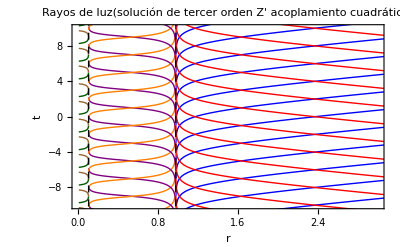

```mathematica
μ2=1;
(*Función métrica de tercer orden*)
f[r2_]:=1+r2^2-(209 r2^(10/3))/(7^(1/3) (-2219 r2^4-2268 μ2+18 √14 √(15174 r2^8+2219 r2^4 μ2+1134 μ2^2))^(1/3))+(r2^(2/3) (-2219 r2^4-2268 μ2+18 √14 √(15174 r2^8+2219 r2^4 μ2+1134 μ2^2))^(1/3))/7^(2/3)
(*Buscar ambas raíces*)
horizons=r/. NSolve[f[r]==0&&r<10&&r>0,r,Reals];
{rInner,rOuter}=Sort[horizons]
rStarExt=NDSolveValue[{y'[r]==1/f[r],y[rOuter+0.001]==0},y,{r,rOuter+0.001,10}];
rStarMid=NDSolveValue[{y'[r]==1/f[r],y[(rInner+rOuter)/2]==0},y,{r,rInner+0.001,rOuter-0.001}];
rStarInt=NDSolveValue[{y'[r]==1/f[r],y[rInner-0.001]==0},y,{r,0.001,rInner-0.001}];
plotExt=Plot[Evaluate[Table[{rStarExt[r]+c,-rStarExt[r]+c},{c,-15,15,2}]],{r,rOuter+0.001,4},PlotStyle->{Directive[Blue,Thin],Directive[Red,Thin]}];
plotMid=Plot[Evaluate[Table[{rStarMid[r]+c,-rStarMid[r]+c},{c,-15,15,2}]],{r,rInner+0.001,rOuter-0.001},PlotStyle->{Directive[Purple,Thin],Directive[Orange,Thin]}];
plotInt=Plot[Evaluate[Table[{rStarInt[r]+c,-rStarInt[r]+c},{c,-15,15,2}]],{r,0.001,rInner-0.001},PlotStyle->{Directive[DarkGreen,Thin],Directive[Brown,Thin]}];
plotf3primcuad=Show[plotExt,plotMid,plotInt,Frame->True,FrameLabel->{"r","t"},PlotRange->{{0,3},{-10,10}},PlotLabel->"Rayos de luz(solución de tercer orden Z' acoplamiento cuadrático)",Epilog->{{Dashed,Black,InfiniteLine[{rOuter,0},{0,1}]},{Dashed,Black,InfiniteLine[{rInner,0},{0,1}]}}]
```

```mathematica
Export["Conos de Luz f3primcuad5D.png",plotf3primcuad]
```

Conos de Luz f3primcuad5D.png

### Acoplamiento b=4 Zprim

```mathematica
Clear["Global`*"]
```

{0.0522512,0.994569}

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

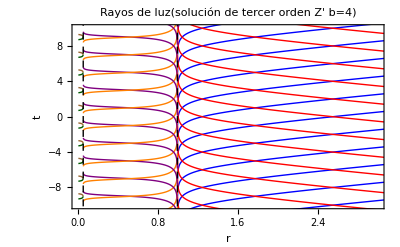

```mathematica
μ2=1;
b=4;
(*Función métrica de tercer orden*)
f[r2_]:=1+r2^2+((7-216 b) r2^(10/3))/( 7^(1/3)(-7*(-7+324 b) r2^4-(972 7^(2/3) (-7+288 b) (49+108 b (-21+√21 √(-7+288 b)))^(4/3) b μ2)/((93312 b^2+7 √21 √(-7+288 b)-324 b (7+√21 √(-7+288 b))) (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3)))+18*42^(1/2) √( 18(-7+288 b) b^2 r2^8+(7^(2/3) (-7+324 b) (-7+288 b)(49+108 b (-21+√21 √(-7+288 b)))^(4/3)b r2^4 μ2)/((93312 b^2+7 √21 √(-7+288 b)-324 b (7+√21 √(-7+288 b))) (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3)))+(486 7^(1/3)   b^2 (-7+288 b)^2(49+108 b (-21+√21 √(-7+288 b)))^(8/3) μ2^2)/((93312 b^2+7 √21 √(-7+288 b)-324 b (7+√21 √(-7+288 b)))^2 (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3))^2)))^(1/3))+r2^(2/3)/7^(2/3)(-7*(-7+324 b) r2^4-(972 7^(2/3) (-7+288 b) (49+108 b (-21+√21 √(-7+288 b)))^(4/3) b μ2)/((93312 b^2+7 √21 √(-7+288 b)-324 b (7+√21 √(-7+288 b))) (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3)))+18*42^(1/2) √( 18(-7+288 b) b^2 r2^8+(7^(2/3) (-7+324 b) (-7+288 b)(49+108 b (-21+√21 √(-7+288 b)))^(4/3)b r2^4 μ2)/((93312 b^2+7 √21 √(-7+288 b)-324 b (7+√21 √(-7+288 b))) (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3)))+(486 7^(1/3)   b^2 (-7+288 b)^2(49+108 b (-21+√21 √(-7+288 b)))^(8/3) μ2^2)/((93312 b^2+7 √21 √(-7+288 b)-324 b (7+√21 √(-7+288 b)))^2 (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3))^2)))^(1/3)
(*Buscar ambas raíces*)
horizons=r/. NSolve[f[r]==0&&r<10&&r>0,r,Reals];
{rInner,rOuter}=Sort[horizons]
rStarExt=NDSolveValue[{y'[r]==1/f[r],y[rOuter+0.001]==0},y,{r,rOuter+0.001,10}];
rStarMid=NDSolveValue[{y'[r]==1/f[r],y[(rInner+rOuter)/2]==0},y,{r,rInner+0.001,rOuter-0.001}];
rStarInt=NDSolveValue[{y'[r]==1/f[r],y[rInner-0.001]==0},y,{r,0.001,rInner-0.001}];
plotExt=Plot[Evaluate[Table[{rStarExt[r]+c,-rStarExt[r]+c},{c,-15,15,2}]],{r,rOuter+0.001,4},PlotStyle->{Directive[Blue,Thin],Directive[Red,Thin]}];
plotMid=Plot[Evaluate[Table[{rStarMid[r]+c,-rStarMid[r]+c},{c,-15,15,2}]],{r,rInner+0.001,rOuter-0.001},PlotStyle->{Directive[Purple,Thin],Directive[Orange,Thin]}];
plotInt=Plot[Evaluate[Table[{rStarInt[r]+c,-rStarInt[r]+c},{c,-15,15,2}]],{r,0.001,rInner-0.001},PlotStyle->{Directive[DarkGreen,Thin],Directive[Brown,Thin]}];
plotf3primb4=Show[plotExt,plotMid,plotInt,Frame->True,FrameLabel->{"r","t"},PlotRange->{{0,3},{-10,10}},PlotLabel->"Rayos de luz(solución de tercer orden Z' b=4)",Epilog->{{Dashed,Black,InfiniteLine[{rOuter,0},{0,1}]},{Dashed,Black,InfiniteLine[{rInner,0},{0,1}]}}]
```

```mathematica
Export["Conos de Luz f3primb45D.png",plotf3primb4]
```

Conos de Luz f3primb45D.png

### Agujero negro regular

```mathematica
Clear["Global`*"]
```

0.383388

10

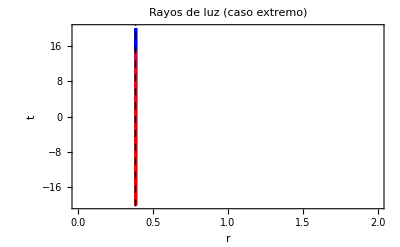

0.383388

```mathematica
μ=0.358787182711;
(*Función métrica de tercer orden*)
f[r_]:=1+r^2+(r^(2/3) (-1085 r^4+18 (-63 μ+√7 √(3699 r^8+1085 r^4 μ+567 μ^2)))^(1/3))/7^(2/3)-(101 r^(10/3))/((-7595 r^4+126 (-63 μ+√7 √(3699 r^8+1085 r^4 μ+567 μ^2)))^(1/3))
(*Buscar la raíz*)
rh=r/. FindRoot[f[r]==0,{r,0.5}]
eps=0.05;
scale=10
rStar=NDSolveValue[{y'[r]==1/f[r],y[rh+eps]==0},y,{r,rh+eps,4},MaxStepSize->0.001];
plotExtreme=Plot[Evaluate[Table[{scale*rStarExt[r]+c,-scale*rStarExt[r]+c},{c,-15,15,2}]],{r,rh+0.001,rh+1},PlotRange->{{0,2},{-20,20}},PlotStyle->{Blue,Red},Frame->True,FrameLabel->{"r","t"},PlotLabel->"Rayos de luz (caso extremo)",Epilog->{{Dashed,Thick,Black,InfiniteLine[{rh,0},{0,1}]}}]
```